## (*--Salamander/Newt Model--*)

## (*--Setup--*)

### (*--Load libraries--*)

```mathematica
(*--Load libraries and define objects--*)

(*<<LinearAlgebra`MatrixManipulation`
<<Graphics`Animation`
<<Graphics`PlotField`*)

(*--Load libraries and define objects--*)
<<ivamatica/defpackages.m;
LoadPackages[TPRINCIPAL]
DoneLoading

(* Additional basic math functions. *)
<<ivamatica/Basic/extras.m

(* For dealing with equations of motions. *)
<<ivamatica/Dynamics/averaging.m
<<ivamatica/Dynamics/equations.m

(* Lagrangian mechanics. *)
<<ivamatica/Mechanics/constraints.m
<<ivamatica/Mechanics/kinematics.m
<<ivamatica/Mechanics/lagrangian.m


(* For creating visual movie output. *)
<<ivamatica/Graphics/anim.m

(*<<mathematica/libs/configuration.m
CO = Configuration;*)
```

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer, val_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oSet[IntegerDigits[_, 2, b], val_Integer] is Protected.

General::stop: Further output of UpSetDelayed :: write will be suppressed during this calculation.

Loaded Euclidean package 
Loaded Fiber Bundles package 
Loaded Manifolds package 
Loaded Vectors package 
Loaded Tangents package 
Loaded Tangent Fiber Bundles package 
Loaded Tangent Manifolds package 
Loaded Lie Groups package 
Loaded Tangent Lie Groups package 
Loaded Principal Bundles package 
Loaded Tangent Principal Bundles package

Removed package loading variables.

```mathematica
M = Euclidean;
TM = TEuclidean;

G=SE2;
𝔤 = se2;
SuperStar[𝔤] = dse2;
TG = TSE2;
tG = SE2xse2;
dG = SE2xdse2;
Q=ExSE2;
TQ = TExTSE2;
```

### (*--Configuration Space.--*)

```mathematica
g = oInit[G, {x, y, θ}];
dimG = gDim[g];
g' = oInit[Vector, Table[ gLocal[g][[i]]', {i, dimG}]];
vg = oInit[TG, g, g'];

r = oInit[M, {r1}];
dimM = gDim[r];
r' = oInit[Vector,Table[ gLocal[r][[i]]' , {i, dimM}]];

q = oInit[Q, r, g];
dimQ = dimM + dimG;
q' = {r', g'};

vq = oInit[TQ, q,{r', g'}]

ξ = oInit[𝔤, {ξ1, ξ2, ξ3}];
```

Tangent Vector {{r1'}, {x', y', θ'}} of principal fiber bundle at the point {{r1}, {x, y, θ}}

```mathematica
L = 3/20;
w = 3/100;
β[M[r_],s_] :=  oInit[G, {0,0, -ArcTan[ -(r[[1]] π)/L Cos[(π 0)/L]]}]·oInit[G,{-s , r[[1]] Sin[ (π s)/L ]  , ArcTan[ -(r[[1]] π)/L Cos[(π s)/L]]}]
```

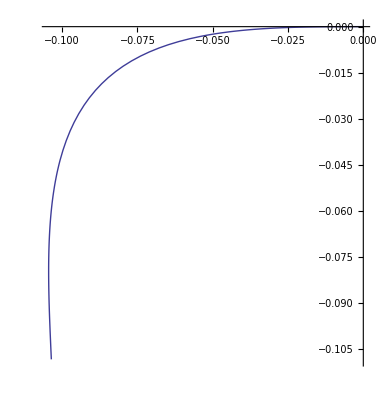

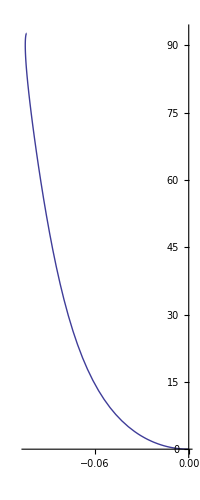

```mathematica
pr = oInit[M, {0.05}];
ParametricPlot[{gLocal[β[pr,s]][[1]], gLocal[β[pr,s]][[2]]}, {s, 0, L}, AspectRatio -> Automatic, PlotRange -> All]
ParametricPlot[{gLocal[β[pr, s]][[1]], 180/π gLocal[β[pr, s]][[3]]}, {s, 0, L}, PlotRange -> All]
```

## (*--Equations of Motion--*)

### (*--Compute Connection Form.--*)

```mathematica
gB[M[r_], s_] := g · β[M[r],s]
gl = oInit[G, {0, w, 0}];
gr = oInit[G, {0,-w,0}];
```

```mathematica
gfl = gB[r, 0] · gl;
gfr = gB[r, 0] · gr;
gbl = gB[r, L] · gl;
gbr = gB[r, L] · gr;
```

```mathematica
gfl' = D[gLocal[gfl], q] vq;
gfr' = D[gLocal[gfr], q] vq;
gbl' = D[gLocal[gbl], q] vq;
gbr' = D[gLocal[gbr], q] vq;
```

```mathematica
ξfl = cReduce[gfl', vg, ξ];
ξfr = cReduce[gfr', vg, ξ];
ξbl = cReduce[gbl', vg, ξ];
ξbr = cReduce[gbr', vg, ξ];
```

```mathematica
sol13 = Solve[{ξfl[[1]] == 0, ξfl[[2]] == 0, ξbr[[2]] == 0}, gLocal[ξ]] // Simplify;

sol24 = Solve[{ξfr[[1]] == 0, ξfr[[2]] == 0, ξbl[[2]] == 0}, gLocal[ξ]] // Simplify;
```

```mathematica
𝒜13 =Flatten[- gLocal[ξ] /. sol13];
𝒜24 =Flatten[- gLocal[ξ] /. sol24];
```

## (*--Simulations--*)

### (*--Open Loop Locomotion--*)

```mathematica
Clear[rt, rpt]
rt[t_]  := oInit[M, {0.01+0.015 Sin[t]}]
rpt[t_] := oInit[Vector,D[gLocal[rt[x]], x]/.{x->t}]
```

```mathematica
𝒜13t = oInit[𝔤, 𝒜13 /. {gLocal[r][[1]] -> gLocal[rt[t]][[1]], gLocal[r'][[1]] -> gLocal[rpt[t]][[1]]} // Simplify];
𝒜24t = oInit[𝔤, 𝒜24 /. {gLocal[r][[1]] -> gLocal[rt[t]][[1]], gLocal[r'][[1]] -> gLocal[rpt[t]][[1]]} // Simplify];
```

```mathematica
v1[tt_] := Which[ Mod[tt, 2 π ] ≤ π/2, 1, Mod[tt, 2 π] ≥ (3 π)/2, 1, True, 0];
v2[tt_] := Which[(Mod[tt, 2 π] ≥ π/2) && (Mod[tt, 2 π] ≤ (3 π)/2) , 1, True , 0];
```

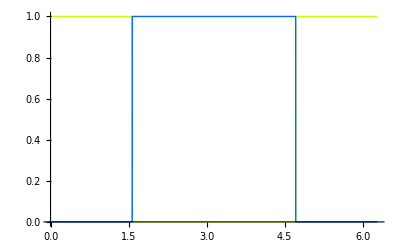

```mathematica
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle -> {Hue[0.2], Hue[0.6]}]
```

```mathematica
gdes[t_] := oInit[G, {0,0,0}];
g0 = oInit[G, {0,0,0}];
t0 = 0; t1 = 30 π;
solved = NDSolve[ -v2[t]𝒜13t - v1[t] 𝒜24t, g0, g, {t,t0,t1}, MaxSteps ->10000]
gcurr = oInit[G, Table[(gLocal[g][[i]][t1] /.solved)[[1]], {i, dimG}]]
(*solved2 = oNDSolve[g, -𝒜24t, gcurr, {t, π/2, π}]
gcurr2 = oInit[G, Table[(gLocal[g][[i]][π] /.solved2)[[1]], {i, dimG}]]*)
```

{{x→InterpolatingFunction[{{0.,94.2478}},<>],y→InterpolatingFunction[{{0.,94.2478}},<>],θ→InterpolatingFunction[{{0.,94.2478}},<>]}}

(0.294538
-0.371039
-1.56099)

```mathematica
gft[t_] := oInit[G, Table[(gLocal[g][[i]][t] /.solved)[[1]], {i, dimG}]]
rft[t_] := oInit[M, {gLocal[rt[t]][[1]], v2[t], v1[t], v2[t], v1[t]}]
```

```mathematica
qft[t_] := oInit[Q, rft[t], gft[t]]
```

```mathematica
βft[t_, s_] := β[rft[t], s]
```

```mathematica
tot[t_, s_] := {gLocal[(gft[t] · βft[t, s])][[1]], gLocal[(gft[t] · βft[t, s])]  [[2]]}
tot[0,0]
```

{0.,0.}

### (*--Lie Group Control--*)

```mathematica
(*--Trajectory Selection--*)

despath = 1;
Clear[α];
Which[despath == 1, k = {-0.25,  -0.01,-0.01}, despath == 2, k ={-0.25,  -0.01,-0.01} ];
errF[G[gerr_]] := Module[ {f1, f2} , 
f1 =-k[[1]] gerr[[1]];
f2 = ( k[[2]] ArcTanH[ gerr[[1]], gerr[[2]] ] + k[[3]] gerr[[3]]);
{f1, f2}
]
```

```mathematica
(*--Define body kinematics with control parametrization.--*)

ω=1;
ϵ=1;
Τ = (2 π ϵ)/ω;
Clear[rt, rpt]
rt[t_, al_]  := oInit[M, {al[[2]]+al[[1]] ϵ/ω Sin[(ω t)/ϵ]}]
rpt[t_, al_] := oInit[Vector,D[gLocal[rt[x, al]], x]/.{x->t}]
```

```mathematica
(*--Solve time-varying connection form given body trajectories.--*)

𝒜13t[al_] := oInit[𝔤, 𝒜13 /. {gLocal[r][[1]] -> gLocal[rt[t,al]][[1]], gLocal[r'][[1]] -> gLocal[rpt[t,al]][[1]]} // Simplify];
𝒜24t[al_] := oInit[𝔤, 𝒜24 /. {gLocal[r][[1]] -> gLocal[rt[t,al]][[1]], gLocal[r'][[1]] -> gLocal[rpt[t,al]][[1]]} // Simplify];
```

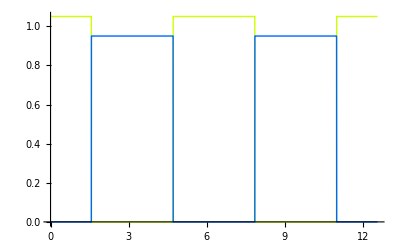

```mathematica
(*--Foot activation functions.--*)

v1[tt_] := Which[ Mod[tt, 2 π ] ≤ π/2, 1, Mod[tt, 2 π] ≥ (3 π)/2, 1, True, 0];
v2[tt_] := If[(Mod[tt, 2 π] >  π/2) && (Mod[tt, 2 π] <  (3 π)/2) , 1, 0];
Plot[{1.05v1[t],0.95 v2[t]}, {t, 0, 4π}, PlotStyle -> {Hue[0.2], Hue[0.6]}]
```

```mathematica
g0=oInit[G,{-1,-0.5,- π/5}];
g0 = oInit[G, {0,0,0}];
Which[  
despath == 1,gdes[t_] := oInit[G, {1/200 t,0,0}],
despath == 2, gdes[t_] := oInit[G, {1/(200 √2) t, 1/(200 √2) t, ArcTan[1/(20 √2), 1/(20 √2)]}]];
```

```mathematica
gcurr=g0;
gflow=Append[{},gcurr];
αmax = .05;

αflow = {};
xflow = {};
rflow = {};

maxsteps=1;
t0 = 0; t1 = maxsteps * Τ;

For[cnt=1,cnt<=maxsteps,cnt++,
α = {αmax/2,0};(*errF[Inverse[gcurr] ·gdes[cnt*Τ]];*)
Which[α[[1]] > αmax, α[[1]] = αmax, α[[1]] < -αmax, α[[1]] = -αmax];
Which[α[[2]] >αmax, α[[2]] =αmax, α[[2]] < -αmax, α[[2]] = -αmax];
gsol[cnt] = NDSolve[ -v2[(ω t)/ϵ]𝒜13t[α] -v1[(ω t)/ϵ] 𝒜24t[α], gcurr, g, {t,0, Τ}];
gcurr=oInit[G,Flatten[Table[gLocal[g][[i]][Τ]/.gsol[cnt],{i,1,gDim[g]}]]];
gflow=Append[gflow,gcurr];
αflow = Append[αflow, α];

rflow = Append[rflow, rt[(ω t)/ϵ] ];
]; (* This loop is not DETERMINISTIC!!!! Something is wrong with the Solver.*)
N[{gcurr, gdes[t1],Inverse[gcurr] ·gdes[cnt*Τ]}]
```

{(-6.61437×10^-9
-1.08559×10^-9
-2.04481×10^-7),(0.0314159
0.
0.),(0.0628319
1.39335×10^-8
2.04481×10^-7)}

```mathematica
gft[t_]:=Module[{nt,tt},nt=Floor[t/Τ]+1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
oInit[G,Table[(gLocal[g][[i]][tt]/.gsol[nt])[[1]],{i,1,dimG}]]
];

Clear[dist, err];
rft[time_] := Module[{nt, tt}, nt = Floor[time/Τ] + 1;
If[nt≤maxsteps,tt=time-Floor[time/Τ] Τ,nt=maxsteps;
tt=Τ;];
oInit[M,Flatten[{rflow[[nt]][[1]] /. {t -> tt}, v2[(ω tt)/ϵ],v1[(ω tt)/ϵ],v2[(ω tt)/ϵ],v1[(ω tt)/ϵ]}] ]];

qft[t_] := oInit[Q,rft[t], gft[t]];
```

## (*--Testing; Straight and Curvilinear Motion--*)

```mathematica
(*--Added a second harmonic.  It doesn't really add to the functionality.;
  A better approach would be to vary the piecewise holonomic constraints.;
  Will add the shrinking capability, however.  Just to see.;
--*)
```

```mathematica
g = oInit[G, {x, y, θ}];
dimG = gDim[g];
g' = oInit[Vector, Table[ gLocal[g][[i]]', {i, dimG}]];
vg = oInit[TG, g, g'];

r = oInit[M, {r1, r2, r3}];
dimM = gDim[r];
r' = oInit[Vector,Table[ gLocal[r][[i]]' , {i, dimM}]];

q = oInit[Q, r, g];
dimQ = dimM + dimG;
q' = {r', g'};

vq = oInit[TQ, q,{r', g'}]

ξ = oInit[𝔤, {ξ1, ξ2, ξ3}];
```

Tangent Vector {{r1', r2', r3'}, {x', y', θ'}} of principal fiber bundle at the point {{r1, r2, r3}, {x, y, θ}}

```mathematica
L = 3/20;
w =L/4;
β[M[r_],s_] :=  oInit[G, {0,0, - ArcTan[ -(r[[1]] π)/(r[[3]]L) Cos[(π 0)/L]-(2 π r[[2]])/(r[[3]]L) Cos[(2 π 0)/L]]}]·oInit[G,{-r[[3]]s , r[[1]] Sin[ (π s)/L ] + r[[2]] Sin[ (2 π s)/L], ArcTan[ -(π r[[1]])/(r[[3]]L) Cos[(π s)/L] -(2 π r[[2]])/(r[[3]] L) Cos[(2 π s)/L]]}]
```

```mathematica
pr = oInit[M, {0, -0.01, 1}];
ParametricPlot[{gLocal[β[pr,s]][[1]], gLocal[β[pr,s]][[2]]}, {s, 0, L}, AspectRatio -> Automatic]
ParametricPlot[{s + 0 gLocal[β[pr, s]][[1]], 180/π gLocal[β[pr, s]][[3]]}, {s, 0, L}]
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
gB[M[r_], s_] := g · β[M[r],s]
gl = oInit[G, {0, w, 0}];
gr = oInit[G, {0,-w,0}];
```

```mathematica
gfl = gB[r, 0] · gl;
gfr = gB[r, 0] · gr;
gbl = gB[r, L] · gl;
gbr = gB[r, L] · gr;
```

```mathematica
gfl' = D[gLocal[gfl], q] vq;
gfr' = D[gLocal[gfr], q] vq;
gbl' = D[gLocal[gbl], q] vq;
gbr' = D[gLocal[gbr], q] vq;
```

```mathematica
ξfl = cReduce[gfl', vg, ξ];
ξfr = cReduce[gfr', vg, ξ];
ξbl = cReduce[gbl', vg, ξ];
ξbr = cReduce[gbr', vg, ξ];
```

```mathematica
sol13 = Solve[{ξfl[[1]] == 0, ξfl[[2]] == 0, ξbr[[2]] == 0}, gLocal[ξ]] // Simplify;

sol24 = Solve[{ξfr[[1]] == 0, ξfr[[2]] == 0, ξbl[[2]] == 0}, gLocal[ξ]] // Simplify;

sol12 = Solve[{ξfl[[1]] == 0, ξfl[[2]] == 0, ξfr[[1]] == 0}, gLocal[ξ]] // Simplify;

sol34 = Solve[{ξbl[[1]] == 0, ξbl[[2]] == 0, ξbr[[1]] == 0}, gLocal[ξ]]  // Simplify;
```

```mathematica
ξfl
```

{ξ1-(3 ξ3)/80,ξ2,ξ3}

```mathematica
𝒜13 =Flatten[- gLocal[ξ] /. sol13];
𝒜24 =Flatten[- gLocal[ξ] /. sol24];
𝒜12 =Flatten[- gLocal[ξ] /. sol12];𝒜34 =Flatten[- gLocal[ξ] /. sol34];
```

```mathematica
Clear[rt, rpt]
```

```mathematica
rt[0]
```

rt[0]

```mathematica
Sin[ArcSin[0.15]]
```

0.15

```mathematica
bias = 0;
rt[t_]  := oInit[M, {-0.015-0.007(bias+Sin[t- ArcSin[bias]]), 0,1}]
rpt[t_] := oInit[Vector,D[gLocal[rt[x]], x]/.{x->t}]
```

```mathematica
zsol = NDSolve[ {z'[t] == -20(z[t] - If[ t < 2 π, 0.015, 0]- 0.015 Sin[t]) + 0.015 Cos[t], z[0] == 0},z, {t, 0,4 π}];
Plot[{(z[t] /. zsol)[[1]],0 If[ t < 2 π, 0.015, 0] +0 0.015Sin[t]}, {t, 0, 4 π}, PlotRange -> All]
Plot[{(z'[t] /. zsol)[[1]], 0.015Cos[t]}, {t, 0, 4 π}, PlotRange -> All]
{z[π/2] /.zsol, z'[π/2] /.zsol}
```

⁃Graphics⁃

⁃Graphics⁃

{{0.03},{3.80789×10^-8}}

```mathematica
Plot[gLocal[rt[t]][[1]] , {t, 0, 2 π}]
Plot[gLocal[rpt[t]][[1]] , {t, 0, 2 π}]
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
𝒜13t = oInit[𝔤, 𝒜13 /. Join[Table[gLocal[r][[i]] -> gLocal[rt[t]][[i]],{i, dimM}], Table[ gLocal[r'][[i]] -> gLocal[rpt[t]][[i]], {i, dimM}]] // Simplify];
𝒜24t = oInit[𝔤, 𝒜24 /.Join[Table[gLocal[r][[i]] -> gLocal[rt[t]][[i]],{i, dimM}], Table[ gLocal[r'][[i]] -> gLocal[rpt[t]][[i]], {i, dimM}]]  // Simplify];
feet1 = {1, 0, 1, 0};
feet2 = {0, 1, 0, 1};
```

```mathematica
2 π({α/π, 0, 0}.Table[ D[𝒜13, gLocal[r][[i]]'], {i, dimM}] + {-α/π, 0, 0}.Table[ D[𝒜24, gLocal[r][[i]]'], {i, dimM}] )/. {r3 -> 1, r2 -> 0, r1 -> 0.0, α -> 0.015} // Simplify //N //MatrixForm
```

(0.0471239
0.
0.)

```mathematica
𝒜12t = oInit[𝔤, 𝒜12 /. Join[Table[gLocal[r][[i]] -> gLocal[rt[t]][[i]],{i, dimM}], Table[ gLocal[r'][[i]] -> gLocal[rpt[t]][[i]], {i, dimM}]] // Simplify];
𝒜34t = oInit[𝔤, 𝒜34 /.Join[Table[gLocal[r][[i]] -> gLocal[rt[t]][[i]],{i, dimM}], Table[ gLocal[r'][[i]] -> gLocal[rpt[t]][[i]], {i, dimM}]]  // Simplify];
feet1 = {1, 1, 0, 0};
feet2  = {0,0, 1, 1};
```

```mathematica
locChoice = 4;
Which[locChoice == 1,
v1[tt_] := Which[ Mod[tt, 2π ] ≤ π/2, 1, Mod[tt, 2 π] ≥ (3 π)/2, 1, True, 0];v2[tt_] := Which[(Mod[tt, 2 π] ≥ π/2) && (Mod[tt, 2 π] ≤ (3 π)/2) , 1, True , 0];
, locChoice == 2,
v1[tt_] := If[( Mod[tt, 2π ] ≤π/2) || Mod[tt, 2 π] ≥ (3 π)/2, 1,0];v2[tt_] := If[ (Mod[tt, 2 π] ≥ π/2) &&( Mod[tt, 2 π] ≤ (3 π)/2), 1, 0];
, locChoice == 3,
v1[tt_] := If[ Mod[tt, 2π ] ≤π, 1,0];v2[tt_] := If[ Mod[tt, 2 π] ≥ π, 1, 0];
, locChoice == 4,
  v1[tt_] := If[ (Mod[tt, 2 π] ≤ π/2+ArcSin[bias]) || (Mod[tt, 2 π] ≥ (3 π)/2 + ArcSin[bias]),1, 0];
v2[tt_] := Which[(Mod[tt, 2 π] ≥ π/2 +ArcSin[bias]) && (Mod[tt, 2 π] ≤ (3 π)/2+ArcSin[bias]) , 1, True , 0];
]
```

```mathematica
futChoice = 1;
If[ futChoice == 1, 
𝒜a = 𝒜13t; 𝒜b = 𝒜24t;,
𝒜a = 𝒜12t; 𝒜b = 𝒜34t;];
```

```mathematica
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle -> {Hue[0.2], Hue[0.6]}]
```

⁃Graphics⁃

```mathematica
g0 = oInit[G, {0,0,0}];
t0 = 0; t1 = 20π;
solved = NDSolve[ -v1[t]𝒜a - v2[t] 𝒜b, g0, g,{t,t0,t1}, WorkingPrecision -> 10, MaxSteps -> 10000]
gcurr = oInit[G, Table[(gLocal[g][[i]][t1] /.solved)[[1]], {i, dimG}]]
(*solved2 = oNDSolve[g, -𝒜24t, gcurr, {t, π/2, π}]
gcurr2 = oInit[G, Table[(gLocal[g][[i]][π] /.solved2)[[1]], {i, dimG}]]*)
```

{{x→InterpolatingFunction[{{0.,62.8319}},<>],y→InterpolatingFunction[{{0.,62.8319}},<>],θ→InterpolatingFunction[{{0.,62.8319}},<>]}}

(0.174423
0.0733064
0.800736)

```mathematica
Table[ Plot[ (gLocal[g][[i]][t] /. solved)[[1]], {t, t0, t1}, PlotRange -> All], {i, dimG}]
ParametricPlot[{(gLocal[g][[1]][t] /. solved)[[1]], (gLocal[g][[2]][t] /. solved)[[1]]}, {t, t0, t1}, PlotRange -> All]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

⁃Graphics⁃

```mathematica
gt[t_] := oInit[G, Table[(gLocal[g][[i]][t] /.solved)[[1]], {i, dimG}]]
rt2[t_] := oInit[M, Join[Table[gLocal[rt[t]][[i]], {i, dimM}],feet1 v1[t]+ feet2 v2[t]]]
```

```mathematica
qt[t_] := oInit[Q, rt2[t], gt[t]]
```

```mathematica
rshape[t_] := oInit[M, Join[Table[gLocal[rt[t]][[i]], {i, dimM}],{0,0,0,0}]];
qshape[t_] := oInit[Q, rshape[t], oInit[G, {0,0,0}]]
```

## (*--Visualizing Motion of the Salamander--*)

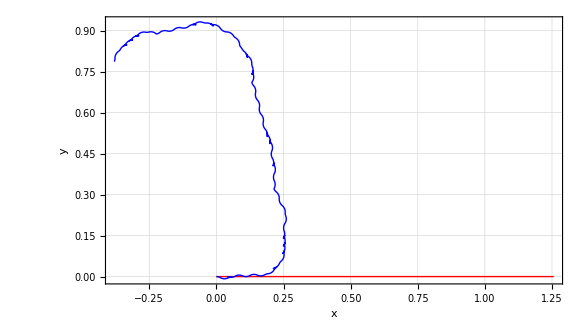

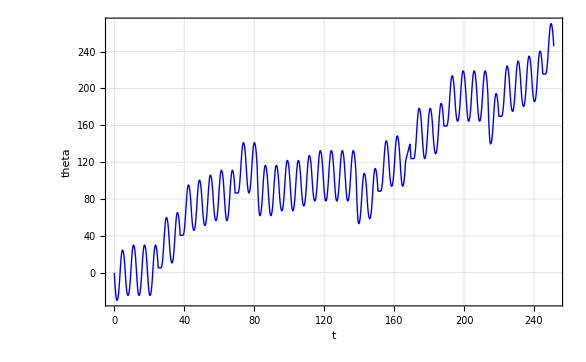

```mathematica
ParametricPlot[{gPosition[gdes[t]],gPosition[gft[t]]},{t,t0, t1},FrameLabel->{"x","y"},PlotRange->All, GridLines->Automatic, PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange -> All, Frame -> True]
Plot[gLocal[gft[t]][[3]]*180/π, {t,t0, t1},Frame->True,FrameLabel->{"t", "theta"},RotateLabel->False, PlotRange->All, GridLines->Automatic, PlotStyle -> {RGBColor[0,0,1]}]
```

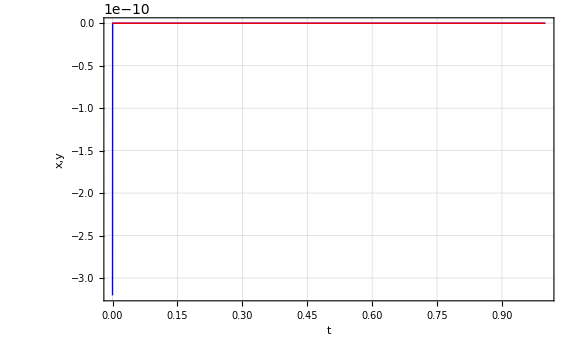

```mathematica
Plot[{gLocal[gft[t]][[1]], gLocal[gft[t]][[2]]}, {t, t0, t1},RotateLabel->False,FrameLabel->{"t", "x,y"},PlotRange->All, GridLines->Automatic, PlotStyle->{RGBColor[0,0,1], RGBColor[1,0,0]}, Frame -> True]
```

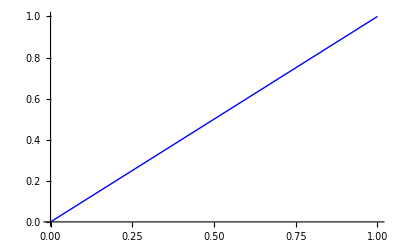

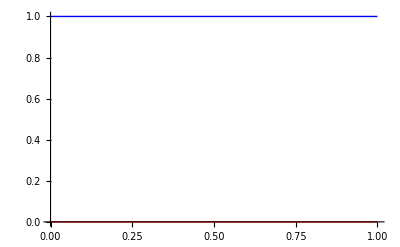

```mathematica
Plot[gLocal[rft[t]][[1]], {t, t0, t1}, PlotStyle -> RGBColor[0,0,1]]
Plot[{gLocal[rft[t]][[2]], gLocal[rft[t]][[3]]},{t, t0, t1} ,PlotStyle ->{ RGBColor[1,0,0],RGBColor[0,0,1]}, PlotRange -> All]
```

## (*--Animating the Salamander--*)

### (*--Define Salamander Graphic--*)

```mathematica
XWIN = 0.3;
YWIN = 0.3;
GRDX= 0.6  {-1,4};
GRDY = 0.6 { -1, 4};
GSTP = .3;
CSTP = .3;
XLen = 5 w;


SalParams = {AspectRatio -> Automatic, Axes -> {False, False}, Frame -> True};


gSalamander[Q[q_], params___] := Module[ {r, g, gfx, x, y, leg1L, leg2L, leg1R, leg2R},
r = oInit[M,Take[gLocal[gBase[Q[q]]], {1, dimM}]];
n = Take[gLocal[gBase[Q[q]]],{dimM+1,gDim[gBase[Q[q]]]}];
g = gGroup[Q[q]];
x = gLocal[g][[1]];
y = gLocal[g][[2]];

body = g · β[r,s];
leg1L = gLocal[body·gl] /. {s -> 0};
leg2L = gLocal[body·gl] /. {s -> L};
leg1R = gLocal[body·gr] /. {s -> 0};
leg2R = gLocal[body·gr] /. {s -> L};
body = gLocal[body];

gfx = {{Thickness[0.01],Line[Table[{body[[1]], body[[2]]}, {s, 0 - L/4, L + (3L)/4, L/20}]]}};
gfx = Append[gfx,Line[{{leg1L[[1]], leg1L[[2]]},{leg1R[[1]], leg1R[[2]]}}] ];
gfx = Append[gfx,Line[{{leg2L[[1]], leg2L[[2]]},{leg2R[[1]], leg2R[[2]]}}] ];

If[n[[1]] == 1 ,gfx = Append[gfx, Disk[{leg1L[[1]],leg1L[[2]]}, 0.007]],gfx = Append[gfx, Circle[{leg1L[[1]],leg1L[[2]]}, 0.007]]];
If[n[[2]] == 1, gfx = Append[gfx,Disk[{leg1R[[1]], leg1R[[2]]}, 0.007]], gfx = Append[gfx,Circle[{leg1R[[1]], leg1R[[2]]}, 0.007]]];
If[n[[3]] == 1, gfx = Append[gfx, Disk[{leg2R[[1]], leg2R[[2]]}, 0.007]], gfx = Append[gfx, Circle[{leg2R[[1]], leg2R[[2]]}, 0.007]]];
If[n[[4]] == 1, gfx = Append[gfx, Disk[{leg2L[[1]],leg2L[[2]]}, 0.007]], gfx = Append[gfx, Circle[{leg2L[[1]],leg2L[[2]]}, 0.007]]];

gfx = Append[gfx,{Dashing[{0.005, 0.02}],fMakeGrid[GRDX, GRDY, GSTP]}];
(*gfx = Append[gfx,Disk[{0,0}, 0.01]];*)



Graphics[gfx /. {w -> 3/100},Join[{ PlotRange->{{0 -XWIN,0+XWIN},{0-YWIN,0+YWIN}}},params]]
];

gSalamander[Q[q_], G[gdes_], params___] := Module[{x, y, θ, gfx, angles, r1, r2, r3},
gc = gGroup[Q[q]];
{x, y} = gPosition[gc];
rc = gBase[Q[q]];

gfx = {gSalamander[Q[q]][[1]]};
plot1 = {gPosition[G[gdes]·oInit[G, {-1/8 XLen , 0, 0}]], gPosition[ G[gdes] ·oInit[G, {1/4 XLen , 0, 0}]]};gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];
gfx=Append[gfx,{RGBColor[0,0,1],Disk[gPosition[G[gdes]],1/40 XLen]}];
plot1 = {gPosition[G[gdes]· oInit[G,{0,1/8 XLen,0}]], gPosition[ G[gdes] ·oInit[G, {0 ,- 1/8 XLen, 0}]]};
gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];
{x, y} = gPosition[G[gdes]];

Graphics[gfx,Join[{ PlotRange->{{x -XWIN,x+XWIN},{y-YWIN,y+YWIN}}}, params]]
]
```

### (*--Snapshots.--*)

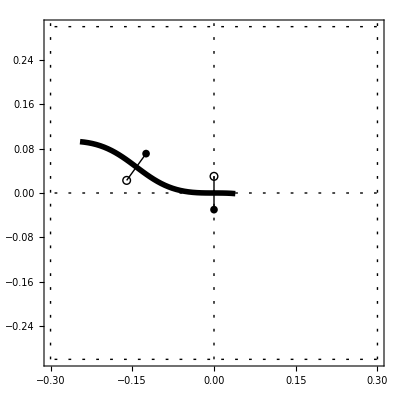

```mathematica
gSalamander[qft[0], SalParams]//Show
```

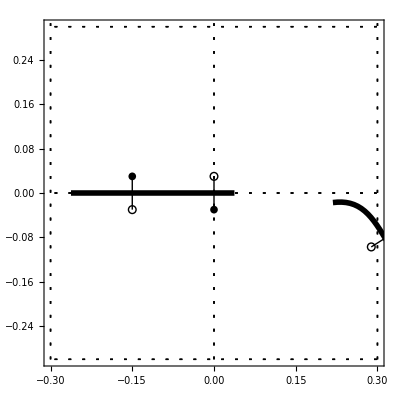

```mathematica
times = Table[ i , {i, t0,t1, (t1-1-t0)/2.23}];
Table[gSalamander[qft[times[[i]]], SalParams], {i, Length[times]}] // Show
```

### (*--Animation--*)

```mathematica
Animate[ gSalamander[qft[t],gdes[t], SalParams], {t,t0,t1, Τ/10}]
```

```mathematica
(*--Exporting the Animation--*)
themovie = Table[ gSalamander[qft[t],gdes[t], Append[SalParams, DisplayFunction -> Identity]], {t,t0,t1, (2π)/10}];
Length[themovie]
fMakeMovie["/home/pvela/tex/talks/BioInspLocomotion/video/salamander/mtmp/","simple_tt",themovie]
```

401